Hawking-Temp von hAlpha, es kommt Self-Encoding raus!!

```mathematica
(* Dies sind die korrekten Rechnungen und Plots der Hawking-TEmp des hAlpha-Modells! *)
```

```mathematica
ClearAll[L,TH,h,Ω,ω,α,α0,g00]
```

```mathematica
h[r_,L_,n_,α_]=1/(1+((L/r)^ α)/2)^ ((3+n)/α);Ω[n_] = 2*Pi^((n+3)/2) / ( Gamma[(n+3)/2]);
ω[n_]=Ω[n]/Ω[0];
α0[n_] = (3+n)/(Log[(2+n)/ω[n]])* Log[(3+n)/2];
LStar[n_]=(1+n)^(-1/α0[n]);(* LStar just for comparing in the end *)
```

```mathematica
g00[r_,n_,L_]=1-2/(n+2) *Ω[0]/Ω[n]*h[r,L,n,α0[n]]/r^(n+1)
```

1-1/(2+n)4 π^(1+1/2 (-3-n)) (1+1/2 (L/r)^(((3+n) Log[(3+n)/2])/Log[2 (2+n) π^(1+1/2 (-3-n)) Gamma[(3+n)/2]]))^(-Log[2 (2+n) π^(1+1/2 (-3-n)) Gamma[(3+n)/2]]/Log[(3+n)/2]) r^(-1-n) Gamma[(3+n)/2]

```mathematica
TH[n_]=1/(4 Pi) * (D[g00[r,n,L], r])/. {L->1}
```

1/(4 π)(-1/(2+n)4 (-1-n) π^(1+1/2 (-3-n)) (1+1/2 (1/r)^(((3+n) Log[(3+n)/2])/Log[2 (2+n) π^(1+1/2 (-3-n)) Gamma[(3+n)/2]]))^(-Log[2 (2+n) π^(1+1/2 (-3-n)) Gamma[(3+n)/2]]/Log[(3+n)/2]) r^(-2-n) Gamma[(3+n)/2]-1/(2+n)2 (3+n) π^(1+1/2 (-3-n)) (1+1/2 (1/r)^(((3+n) Log[(3+n)/2])/Log[2 (2+n) π^(1+1/2 (-3-n)) Gamma[(3+n)/2]]))^(-1-Log[2 (2+n) π^(1+1/2 (-3-n)) Gamma[(3+n)/2]]/Log[(3+n)/2]) (1/r)^(((3+n) Log[(3+n)/2])/Log[2 (2+n) π^(1+1/2 (-3-n)) Gamma[(3+n)/2]]) r^(-2-n) Gamma[(3+n)/2])

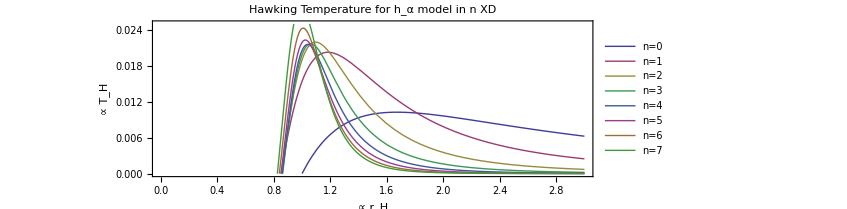

```mathematica
Plot[Evaluate[Table[TH[n],{n,0,7}]],  {r,0,3},PlotRange-> {0,0.025},
PlotLegends->Placed[Table["n="<>ToString[n],{n,0,7}],{Left,Bottom}],Frame->True,FrameLabel->{"∝ r_H","∝ T_H"}, 
AspectRatio->1/3,
PlotLabel->"Hawking Temperature for h_α model in n XD"]
```

```mathematica
(* Check: Wo wird die Hawking-Temp Null? *)
```

```mathematica
Table[Solve[TH[n]==0, r,Reals][[All,1,2]]//N, {n,0,7}]
```

{{1.},{0.850648},{0.856283},{0.861969},{0.859642},{0.851279},{0.839169},{0.824937}}

```mathematica
Table[LStar[n], {n,0,7}]//N
```

{1.,0.850648,0.856283,0.861969,0.859642,0.851279,0.839169,0.824937}

```mathematica
(* ES STIMMTT!!!! Es wird exakt bei L_*=Subscript[r, 0] wenn L=1 null!!! *)
```

Testplot  C=1/T Heat Capacity

```mathematica
Plot[Evaluate[Table[-1/TH[n],{n,0,7}]],  {r,0.5,2},
PlotLegends->Placed[Table["n="<>ToString[n],{n,0,7}],{Right,Top}],
Frame->True,FrameLabel->{"∝ r_H","∝ C"}, 
AspectRatio->1/3,
PlotLabel->"Plot of C ∝ -1/T_H"]
```